```mathematica
ClearAll["Global`*"];
```

## Waveform from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
```

```mathematica
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
```

```mathematica
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-Alpha[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
OMQNM[0, 0]
```

0.291642

```mathematica
(*BOB Waveform calculation*)
```

```mathematica
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[Alpha[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-Alpha[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]],αb[α1, α2]]
```

```mathematica
K[α1_, α2_, t0_, tp_]:=(OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/(1-Tanh[(t0-tp)/TAO[α1, α2]])
Kp[α1_, α2_, t0_, tp_]:=(OMREF[α1, α2]^4 +K[α1, α2, t0, tp](1- Tanh[(t0-tp)/TAO[α1, α2]]))^(1/4)
Km[α1_, α2_, t0_, tp_]:=(OMREF[α1, α2]^4 -K[α1, α2, t0, tp](1+ Tanh[(t0-tp)/TAO[α1, α2]]))^(1/4)
```

```mathematica
OM[α1_, α2_, t0_, tp_, t_]:=  (OMREF[α1, α2]^4 + K[α1, α2, t0, tp](Tanh[(t-tp)/TAO[α1, α2]] -Tanh[(t0-tp)/TAO[α1, α2]]))^(1/4)
```

```mathematica
News[α1_, α2_, t0_, tp_, t_]:= Ap[α1, α2]Sech[(t-tp)/TAO[α1, α2]]/(OM[α1, α2, t0, tp, t])
```

```mathematica
ArcTanp[α1_, α2_, t0_, tp_, t_]:= Kp[α1, α2, t0, tp]  TAO[α1, α2](ArcTan[OM[α1, α2, t0, tp, t]/Kp[α1, α2, t0, tp]] - ArcTan[OMREF[α1, α2]/Kp[α1, α2, t0, tp]])
ArcTanm[α1_, α2_, t0_, tp_, t_]:= Km[α1, α2, t0, tp]  TAO[α1, α2](ArcTan[OM[α1, α2, t0, tp, t]/Km[α1, α2, t0, tp]] - ArcTan[OMREF[α1, α2]/Km[α1, α2, t0, tp]])
ArcTanhp[α1_, α2_, t0_, tp_, t_]:= Kp[α1, α2, t0, tp]  TAO[α1, α2](ArcTanh[OM[α1, α2, t0, tp, t]/Kp[α1, α2, t0, tp]] - ArcTanh[OMREF[α1, α2]/Kp[α1, α2, t0, tp]])
ArcTanhm[α1_, α2_, t0_, tp_, t_]:= Km[α1, α2, t0, tp]  TAO[α1, α2](ArcTanh[OM[α1, α2, t0, tp, t]/Km[α1, α2, t0, tp]] - ArcTanh[OMREF[α1, α2]/Km[α1, α2, t0, tp]])
```

```mathematica
Phi[α1_, α2_, t0_, tp_, t_]:= ArcTanp[α1, α2, t0, tp, t]+ ArcTanhp[α1, α2, t0, tp, t]-ArcTanm[α1, α2, t0, tp, t]- ArcTanhm[α1, α2, t0, tp, t]
```

```mathematica
FindMaximum[(Ap[0, 0]Sech[t/TAO[0,0]])/(OM[0, 0,-50, 0, t])^2,{t,0}][[1]]
```

1.59799

```mathematica
hp[α1_, α2_, t0_, tp_, t_]:= Ap[α1, α2] Sech[(t-tp)/TAO[α1, α2]]/(4(OM[α1, α2, t0, tp, t])^2)Cos[2Phi[α1, α2, t0, tp, t]]
```

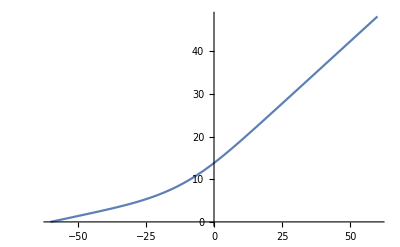

```mathematica
Plot[2(Phi[0, 0, -60, 0, t]), {t, -60,60}]
```

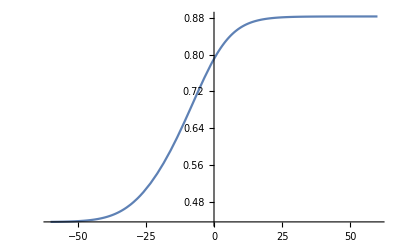

```mathematica
Plot[2(OM[0, 0, -60, 0, t]+0.15), {t, -60,60}]
```

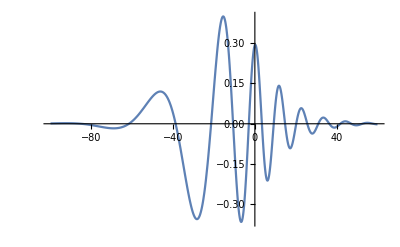

```mathematica
Plot[hp[0, 0, -50, 0, t], {t, -100,60},PlotRange->Full]
```

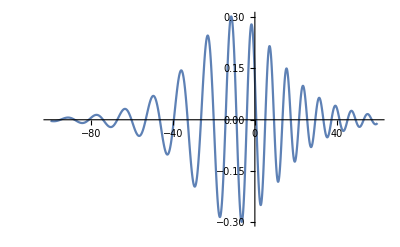

```mathematica
Plot[hp[0.9, 0.9, -245, 0, t], {t, -100,60},PlotRange->Full]
```

```mathematica
(*Define Spin weighted spherical harmomic for 22 mode*)
```

```mathematica
m2Y22[θ_,ϕ_ ]:=1/8 √(5/π)(1+Cos[θ])^2 Exp[2 I ϕ]
Y22[θ_,ϕ_ ]:=1/4 √(15/(2π))(Sin[θ])^2 Exp[2 I ϕ]
m2Y22C[θ_,ϕ_ ]:=1/8 √(5/π)(1+Cos[θ])^2 Exp[-2 I ϕ]
Y22C[θ_,ϕ_ ]:=1/4 √(15/(2π))(Sin[θ])^2 Exp[-2 I ϕ]
```

```mathematica
p[θ_, ϕ_,α1_, α2_, t0_, tp_, t_]:= Re[Y22[θ,ϕ]Ap[α1, α2] Sech[(t-tp)/TAO[α1, α2]]/(2OM[α1, α2, t0, tp, t]) Exp[2 I Phi[0.9, 0.9, -100, 0, t]]]-  m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(t-tp)/TAO[α1, α2]]/(2OM[α1, α2, t0, tp, t]))^2
```

```mathematica
(*Equation 2.21 and 2.23 in Notes*)
```

```mathematica
Q[θ_, ϕ_,α1_, α2_, t0_, tp_, t_]:= -m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2]Sech[(t-tp)/TAO[α1, α2]])^2/(8 OM[α1, α2, t0, tp, t]^3)
```

```mathematica
P[θ_, ϕ_,α1_, α2_, t0_, tp_, t_] := NIntegrate[p[θ, ϕ,α1, α2, t0, tp, x], {x, t0, t}]
```

```mathematica
P1 = Plot[P[0, 0,0, 0, -50, 0, t], {t, -50, 40},PlotLegends->LineLegend[{Blue},{"LHS"}],PlotStyle->Blue];
```

```mathematica
P2 =Plot[Q[0, 0,0, 0, -50, 0, t] , {t, -50, 40},PlotLegends->LineLegend[{Red},{"RHS"}],PlotStyle->Red];
```

```mathematica
psi2Dot[θ_, ϕ_,α1_, α2_, t0_, tp_, t_] := m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2]Sech[(t-tp)/TAO[α1, α2]])^2/(4 OM[α1, α2, t0, tp, t]^2)
```

```mathematica
Psi2[θ_, ϕ_,α1_, α2_, t0_, tp_, t_] :=P[θ, ϕ,α1, α2, t0, tp, t]-Q[θ, ϕ,α1, α2, t0, tp, t]
```

```mathematica
P3 =Plot[Psi2[0, 0,0, 0, -50, 0, t] , {t, -50, 40},PlotLegends->Placed[LineLegend[{Blue},{"ψ_2       "}], {0.25,0.4}],PlotStyle->Blue];
```

```mathematica
Psi2BOBeps[θ_, ϕ_,α1_, α2_, t0_, tp_, t_] :=NIntegrate[-  m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(x-tp)/TAO[α1, α2]]/(2OM[α1, α2, t0, tp, x]))^2, {x, t0, t}]
```

```mathematica
Psi2BOBeps2[θ_, ϕ_,α1_, α2_, t0_, tp_, t_] :=NIntegrate[-  m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(x-tp)/TAO[α1, α2]]/(2OM[α1, α2, t0, tp, x]))^2, {x, t0, t}]- 40m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(t-tp)/TAO[α1, α2]]/(2OM[α1, α2, t0, tp, t]))^2 NIntegrate[-  m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(x-tp)/TAO[α1, α2]]/(2OM[α1, α2, t0, tp, x]))^2, {x, t0,t}]
```

```mathematica
(*Psi2BOBeps2[θ_, ϕ_,α1_, α2_, t0_, tp_, t_] :=NIntegrate[-  m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(x-tp)/TAO[α1, α2]]/OM[α1, α2, t0, tp, x])^2, {x, t0, t}]- m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Ap[α1, α2] Sech[(t-tp)/TAO[α1, α2]]/OM[α1, α2, t0, tp, t])^2 NIntegrate[Psi2BOBeps[θ, ϕ,α1, α2, t0, tp, x] , {x, t0,t}]*)
```

```mathematica
P4 = Plot[Psi2BOBeps[0, 0,0, 0, -50, 0, t] , {t, -50, 40},PlotLegends->Placed[LineLegend[{Black},{"ψ_2 = -ϵ       "}], {0.25,0.5}],PlotStyle->Black];
P5 = Plot[Psi2BOBeps2[0, 0,0, 0, -50, 0, t] , {t, -50, 40},PlotLegends->Placed[LineLegend[{Green},{"ψ_2 = -ϵ -(dϵ/dt)∫ϵdt"}], {0.2,0.6}],PlotStyle->Green];
```

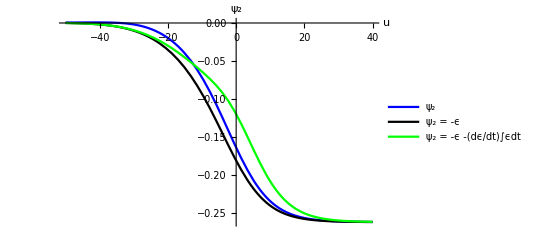

```mathematica
Show[P3,P4, P5, PlotRange-> All, AxesLabel->{u,Subscript[ψ, 2]}]
```

```mathematica
s=NDSolve[{Y''[x]-psi2Dot[0, 0,0, 0, -50, 0, x]==0,Y[0]==0,Y'[0]==0},Y,{x,-50,30}]
```

{{Y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {-52.9982} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

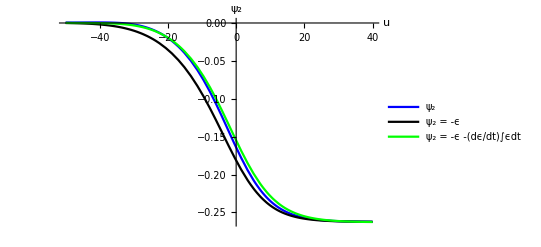

```mathematica
Show[P3, P4,Plot[-Evaluate[{Y'[x-3.0]- Y''[x-3.0]Y[x-3.0]-(Y'[-50]- Y''[-50]Y[-50])}/.s],{x,-50,40},PlotLegends->Placed[LineLegend[{Green},{"ψ_2 = -ϵ -(dϵ/dt)∫ϵdt"}], {0.2,0.6}],PlotStyle->Green],PlotRange-> Full, AxesLabel->{u,Subscript[ψ, 2]}]
```

```mathematica
filelocation="/home/ashok/constraintongwwaveform/data/";
```

```mathematica
StrainData= Import[filelocation<>"EOB_wf.txt","Table"];
```

```mathematica
hData= Transpose[{StrainData[[All,1]], Re[StrainData[[All,2]]Exp[I StrainData[[All,3]]]]}];
```

```mathematica
AmplitudeEOB = Interpolation[Transpose[{StrainData[[All,1]], StrainData[[All,2]]}]];
```

```mathematica
PhaseEOB = Interpolation[Transpose[{StrainData[[All,1]], StrainData[[All,3]]}]];
```

```mathematica
tshiftEOB = FindMaximum[AmplitudeEOB[t]Cos[PhaseEOB[t]],{t,-5}][[2]][[1]][[2]];
```

```mathematica
AmpEOB[t_]:=  AmplitudeEOB[t+tshiftEOB]
```

```mathematica
PhsEOB[t_] := PhaseEOB[t+tshiftEOB]
```

```mathematica
HpEOB[t_] := AmpEOB[t]Cos[PhsEOB[t]]
```

```mathematica
HcEOB[t_] := AmpEOB[t]Sin[PhsEOB[t]]
```

```mathematica
Eob = Plot[HpEOB[t], {t, -60.0, 60.0}, PlotRange->Full, PlotLegends->Placed[LineLegend[{Red},{"EOB"}], {0.1,0.9}],PlotStyle->Red];
```

```mathematica
(*Generate EOB Waveform form LAL*)
```

```mathematica
tshiftBOB = FindMaximum[hp[0.0, 0.0, -50.0, 0, t],{t, -10}][[2]][[1]][[2]];
```

```mathematica
HpBOB[t_] :=  hp[0.0, 0.0, -50.0, 0, t+tshiftBOB]/hp[0.0, 0.0, -50.0, 0, tshiftBOB]
```

```mathematica
Bob = Plot[HpBOB[t], {t, -60,60},PlotRange->Full, PlotLegends->Placed[LineLegend[{Black},{"BOB"}], {0.1,0.8}],PlotStyle->Black];
```

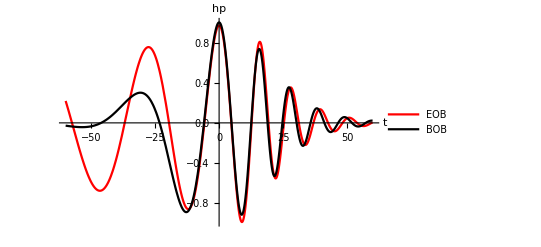

```mathematica
Show[Eob, Bob, PlotRange-> Full, AxesLabel->{"t","hp"}]
```

```mathematica
SigmaEOB[t_]:= HpEOB[t] + I HcEOB[t]
```

```mathematica
pEOB[θ_, ϕ_, t_]:= (Re[Y22[θ,ϕ]D[SigmaEOB[x],x]]-  m2Y22[θ,ϕ]m2Y22C[θ,ϕ](Abs[D[SigmaEOB[x],x]]^2))/.x->t
```

```mathematica
PEOB[θ_, ϕ_,t0_,t_] := NIntegrate[Re[pEOB[θ, ϕ, x]], {x, t0, t}]
QEOB[θ_, ϕ_,t0_,t_] :=(-m2Y22[θ,ϕ]m2Y22C[θ,ϕ]Re[D[SigmaEOB[x],x]Conjugate[SigmaEOB[x]]])/.x->t
```

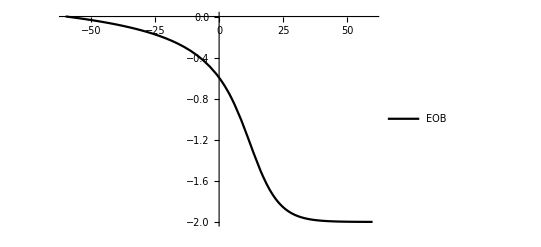

```mathematica
PSIeob = Plot[(PEOB[0,0, -60,t]-QEOB[0,0, -60,t]), {t, -60,60},PlotRange->Full, PlotLegends->Placed[LineLegend[{Black},{"EOB"}], {0.1,0.8}],PlotStyle->Black]
```

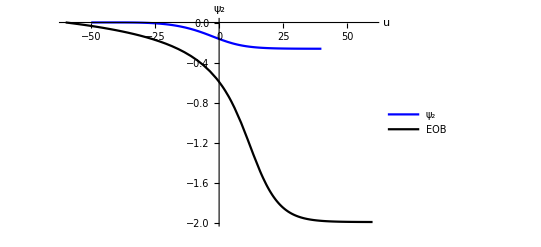

```mathematica
Show[P3,PSIeob,PlotRange-> Full, AxesLabel->{u,Subscript[ψ, 2]}]
```

```mathematica
psi2DotEOB[t_]:=Abs[ D[HpEOB[t] + I HcEOB[t],t]]^2
```

```mathematica
sEOB=NDSolve[{Yeob''[x]-psi2DotEOB[x]==0,Yeob[0]==0,Yeob'[0]==0},Yeob,{x,-60,60}]
```

{{Yeob→InterpolatingFunction[…]}}

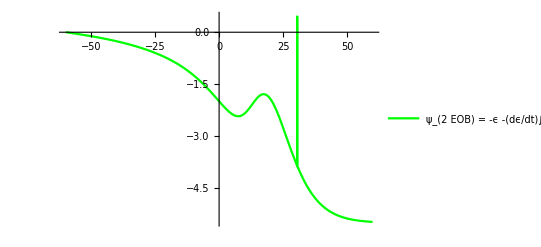

```mathematica
Psi2EOB = Plot[-Evaluate[{((Yeob'[x] -Yeob[x]Yeob''[x])-( Yeob'[-60]-Yeob[-60]Yeob''[-60]))}/.sEOB],{x,-60,60},PlotLegends->Placed[LineLegend[{Green},{"ψ_(2  EOB) = -ϵ -(dϵ/dt)∫ϵdt"}], {0.2,0.6}],PlotStyle->Green]
```

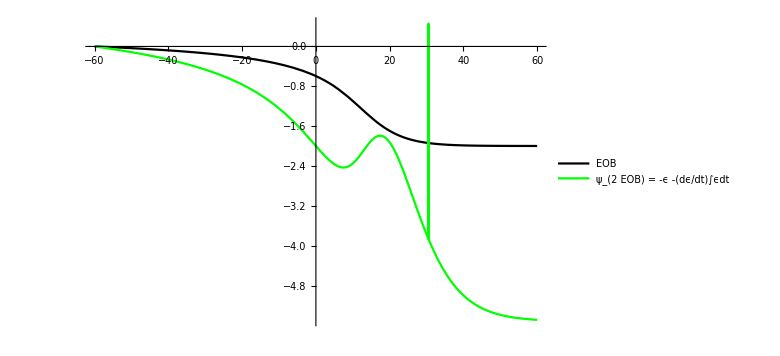

```mathematica
Show[PSIeob, Psi2EOB, PlotRange-> Full]
```